## Change of variables

```mathematica
Gamma[1+1/(2 n)]/.n->4
```

Gamma[9/8]

```mathematica
Integrate[Exp[-g^(2n)/2],{g,-Infinity,Infinity},Assumptions->n>0]
```

$Aborted

```mathematica
Integrate[Exp[-g^8/2],{g,-Infinity,Infinity}]
```

2 2^(1/8) Gamma[9/8]

```mathematica
norm=2^(1/2/n) ((-1)^(2 n))^(-1/2/n) (1+((-1)^(2 n))^(1/2/n)) Gamma[1+1/(2 n)];
norm/.{n->2}
```

2 2^(1/4) Gamma[5/4]

```mathematica
(1+((-1)^(2 n))^(1/(2n)))/.{n->4}
```

2

```mathematica
Integrate[Exp[-g^(2n)/(2 σn^2)],{g,0,Infinity}]
```

ConditionalExpression[2^(1/2/n) (1/σn^2)^(-1/2/n) Gamma[1+1/(2 n)],Re[n]>0&&Re[σn^2]>0]

```mathematica
fg[gt_,n_]:=Exp[-gt^(2n)/2]/(2^(1/(2n))Gamma[1+1/(2n)])
```

```mathematica
Integrate[fg[gt,4],{gt,0,Infinity}]
```

1

```mathematica
Integrate[fg[gt,4],{gt,0,x}]
```

((x^8)^(7/8))/x^7-(x ExpIntegralE[7/8,x^8/2])/(8 2^(1/8) Gamma[9/8])

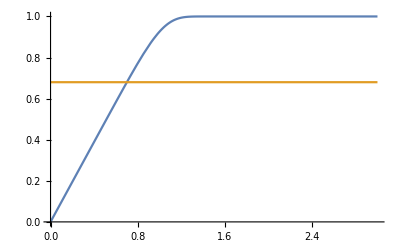

```mathematica
Plot[{((x^8)^(7/8))/x^7-(x ExpIntegralE[7/8,x^8/2])/(8 2^(1/8) Gamma[9/8]),0.68},{x,0,3}]
```

```mathematica
FindRoot[Integrate[fg[gt,4],{gt,0,x}]==0.68,{x,0.5}]
```

{x→0.700586}

### One - sided gaussian - g^4

```mathematica
(* PDF posterior for g4 = g^4, normalized to 1 assuming g^4 >= 0. Here σ4 = 1/√F *)
Integrate[2/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}]
```

1

```mathematica
(* Mean of g4 for the one-sided gaussian https://en.wikipedia.org/wiki/Half-normal_distribution *)
Integrate[2/(√(2π)σ4)g4 Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}]
Integrate[2/(√(2π)σ4)g4 Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}]//N
```

√(2/π) σ4

0.797885 σ4

```mathematica
(* Standard deviation on g4, as expected, see https://en.wikipedia.org/wiki/Half-normal_distribution *)
Simplify[√Integrate[(2(g4-√(2/π) σ4)^2)/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}],Assumptions->{σ4>0}]
Simplify[√Integrate[(2(g4-√(2/π) σ4)^2)/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}],Assumptions->{σ4>0}]//N
```

√((-2+π)/π) σ4

0.60281 σ4

```mathematica
0.6^2
```

0.36

```mathematica
0.7978845608028654 σ4+0.6028102749890869 σ4
```

1.40069 σ4

```mathematica
(* Change of variables from g4 = g^4, to g, check normalization to 1 *)
Integrate[(4 g^3 2)/(√(2π)σ4)Exp[-g^8/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]
```

1

```mathematica
Integrate[(4 g^3 2)/(√(2π)σ4)g Exp[-g^8/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]
Integrate[(4 g^3 2)/(√(2π)σ4)g Exp[-g^8/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]//N
```

(2^(1/8) σ4^(1/4) Gamma[5/8])/(√π)

0.882592 σ4^(1/4)

```mathematica
√Integrate[(4 g^3 2)/(√(2π)σ4)(g-(2^(1/8) σ4^(1/4) Gamma[5/8])/(√π))^2 Exp[-g^8/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]//N
```

0.20787 σ4^(1/4)

```mathematica
0.8825921733858453 σ4^(1/4)+0.20787018579033548 σ4^(1/4)
```

1.09046 σ4^(1/4)

```mathematica
√0.
```

### Full gaussian

```mathematica
(* PDF posterior for g4 = g^4, normalized to 1. Here σ4 = 1/√F *)
Integrate[1/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,-Infinity,Infinity},Assumptions->{σ4>0}]
```

1

```mathematica
(* PDF posterior for g4 = g^4, normalized to 1. Here σ4 = 1/√F *)
(Integrate[1/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,-Infinity,-σ4},Assumptions->{σ4>0}]+Integrate[1/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,σ4,Infinity},Assumptions->{σ4>0}])//N
```

0.317311

```mathematica
(* Mean of g4 for the one-sided gaussian https://en.wikipedia.org/wiki/Half-normal_distribution *)
Integrate[1/(√(2π)σ4)g4 Exp[-g4^2/(2 σ4^2)],{g4,-Infinity,Infinity},Assumptions->{σ4>0}]
Integrate[2/(√(2π)σ4)g4 Exp[-g4^2/(2 σ4^2)],{g4,-Infinity,Infinity},Assumptions->{σ4>0}]//N
```

√(2/π) σ4

0.797885 σ4

```mathematica
(* Standard deviation on g4, as expected, see https://en.wikipedia.org/wiki/Half-normal_distribution *)
Simplify[√Integrate[(2(g4-√(2/π) σ4)^2)/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}],Assumptions->{σ4>0}]
Simplify[√Integrate[(2(g4-√(2/π) σ4)^2)/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}],Assumptions->{σ4>0}]//N
```

√((-2+π)/π) σ4

0.60281 σ4

```mathematica
(* Change of variables from g4 = g^4, to g, check normalization to 1 *)
Integrate[(4 g^3 2)/(√(2π)σ4)Exp[-g^8/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]
```

1

```mathematica
Integrate[(4 g^3 2)/(√(2π)σ4)g Exp[-g^8/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]
Integrate[(4 g^3 2)/(√(2π)σ4)g Exp[-g^8/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]//N
```

(2^(1/8) σ4^(1/4) Gamma[5/8])/(√π)

0.882592 σ4^(1/4)

```mathematica
√Integrate[(4 g^3 2)/(√(2π)σ4)(g-(2^(1/8) σ4^(1/4) Gamma[5/8])/(√π))^2 Exp[-g^8/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]//N
```

0.20787 σ4^(1/4)

### One - sided gaussian - g^2

```mathematica
(* PDF posterior for g4 = g^4, normalized to 1 assuming g^4 >= 0. Here σ4 = 1/√F *)
Integrate[2/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}]
```

1

```mathematica
(* Mean of g4 for the one-sided gaussian https://en.wikipedia.org/wiki/Half-normal_distribution *)
Integrate[2/(√(2π)σ4)g4 Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}]
Integrate[2/(√(2π)σ4)g4 Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}]//N
```

√(2/π) σ4

0.797885 σ4

```mathematica
(* Standard deviation on g4, as expected, see https://en.wikipedia.org/wiki/Half-normal_distribution *)
Simplify[√Integrate[(2(g4-√(2/π) σ4)^2)/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}],Assumptions->{σ4>0}]
Simplify[√Integrate[(2(g4-√(2/π) σ4)^2)/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,0,Infinity},Assumptions->{σ4>0}],Assumptions->{σ4>0}]//N
```

√((-2+π)/π) σ4

0.60281 σ4

```mathematica
(* Change of variables from g4 = g^4, to g, check normalization to 1 *)
Integrate[(2 g 2)/(√(2π)σ4)Exp[-g^4/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]
```

1

```mathematica
Integrate[(2 g 2)/(√(2π)σ4)g Exp[-g^4/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]
Integrate[(2 g 2)/(√(2π)σ4)g Exp[-g^4/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]//N
```

(2^(1/4) √σ4 Gamma[3/4])/(√π)

0.822179 √σ4

```mathematica
√Integrate[(2 g 2)/(√(2π)σ4)(g-(2^(1/4) √σ4 Gamma[3/4])/(√π))^2 Exp[-g^4/(2 σ4^2)],{g,0,Infinity},Assumptions->{σ4>0}]//N
```

0.349151 √σ4

## Back to the χ^2

```mathematica
chiSq=((g^n Sl-Cl)^2)/ΔC^2;
D[chiSq,{g}]
```

(2 g^(-1+n) n Sl (-Cl+g^n Sl))/ΔC^2

```mathematica
Solve[(2 g^(-1+2n) n Sl^2)/ΔC^2==0,g]
```

{{g→0^(1/(-1+2 n))}}

```mathematica
Simplify[(D[chiSq,{g,1}]/.{Cl->Cl0,Cl^2->Cl2})/.{Cl0->0,Cl2->ΔC^2}]
```

(2 g^(-1+2 n) n Sl^2)/ΔC^2

```mathematica
1/2Simplify[(D[chiSq,{g,2}]/.{Cl->Cl0,Cl^2->Cl2})/.{Cl0->0,Cl2->ΔC^2}]
```

(2 g^(-2+2 n) n (-1+2 n) Sl^2)/ΔC^2

```mathematica
1/(3!)Simplify[(D[chiSq,{g,3}]/.{Cl->Cl0,Cl^2->Cl2})/.{Cl0->0,Cl2->ΔC^2}]
```

(4 g^(-3+2 n) n (1-3 n+2 n^2) Sl^2)/ΔC^2

```mathematica
1/(4!)Simplify[(D[chiSq,{g,4}]/.{Cl->Cl0,Cl^2->Cl2})/.{Cl0->0,Cl2->ΔC^2}]/.{n->2}
```

Sl^2/ΔC^2

```mathematica
1/(5!)Simplify[(D[chiSq,{g,5}]/.{Cl->Cl0,Cl^2->Cl2})/.{Cl0->0,Cl2->ΔC^2}]/.{n->4}
```

(56 g^3 Sl^2)/ΔC^2

```mathematica
D[chiSq,{g,4}]/.{g->0}
```

-(48 Ca Cobs)/ΔC^2

```mathematica
D[chiSq,{g,8}](*/.{g->0}*)
```

(40320 Ca^2)/ΔC^2

```mathematica
40320/4!
```

1680

```mathematica
(1632 Ca^2 g^4-48Cobs Ca +48 Ca^2 g^4)/ΔC^2
```

```mathematica
chiSq=(g Ca-Cobs)^2/ΔC^2;
D[chiSq,{g,2}]
```

(2 Ca^2)/ΔC^2

```mathematica
chiSqExp=
```

```mathematica
D[1/(√(2π)σ4)Exp[-g4^2/(2 σ4^2)],{g4,2}]/.{g4->0}
```

-1/(√(2 π) σ4^3)

```mathematica
Solve[(2(g^4 Ca-Cobs)4 g^3 Ca)/ΔCa^2==0,g]
```

{{g→0},{g→0},{g→0},{g→-Cobs^(1/4)/Ca^(1/4)},{g→-(ⅈ Cobs^(1/4))/Ca^(1/4)},{g→(ⅈ Cobs^(1/4))/Ca^(1/4)},{g→Cobs^(1/4)/Ca^(1/4)}}

```mathematica
Simplify[((4 g^3 Ca)^2)/ΔCa^2/.{g->Cobs^(1/4)/Ca^(1/4)}]
```

(16 √Ca Cobs^(3/2))/ΔCa^2

```mathematica
norm=Integrate[Exp[-1/2(g^8/σ4^2+g^4/σ2^2)],{g,0,Infinity},Assumptions->{Re[σ2^2]>0&&Re[σ4^2]>0}]
```

(2^(1/8) Gamma[9/8] Hypergeometric1F1[1/8,1/2,σ4^2/(8 σ2^4)])/((1/σ4^2)^(1/8))-(Gamma[5/8] Hypergeometric1F1[5/8,3/2,σ4^2/(8 σ2^4)])/(8 2^(3/8) σ2^2 (1/σ4^2)^(5/8))